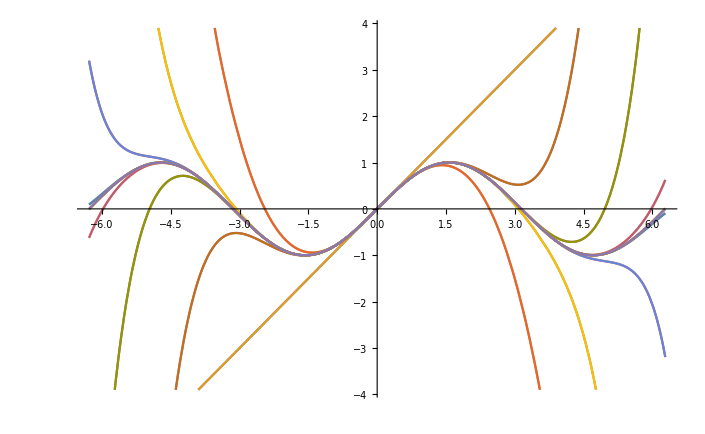

```mathematica
Plot[Evaluate[Table[Normal[Series[Sin[x],{x,0,n}]],{n,20}]],{x,-2Pi,2Pi}]
```

```mathematica
Manipulate[Plot[{Sin[x],Evaluate[Table[Normal[Series[Sin[x],{x,0,m}]],{m,2n-1}]]},{x,-3Pi,3Pi},
Filling->{1->{2n-1}},
PlotRange->3,AspectRatio->Automatic],{n,1,20,1}]
```

```mathematica
Manipulate[Plot[{Evaluate[FourierTrigSeries[π/4Sign[x],x,n]],π/4Sign[Mod [(x+π),2π]-π]},{x,-2π,2π},PlotRange->1,AspectRatio->Automatic],{n,1,20,1}]
```

```mathematica
Normal[Series[Exp[x],{x,0,9}]]
%/.x->1
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880

98641/36288